```mathematica
PulleyTakeup[centerdist_, rpulley_]:= 2 * Sqrt[(centerdist/2)^2 - rpulley^2];
TempPulleyAngle[centerdist_, rpulley_]:= ArcCos[2*rpulley/(centerdist)];
DrivingPulleyAngle[armdist_,ydist_, centerdist_, rpulley_]:= Mod[(2*Pi + (Sign[armdist] * ArcCos[(armdist^2 + (ydist+rpulley)^2 - centerdist^2 - rpulley^2)/(-2 * centerdist * rpulley)] - TempPulleyAngle[centerdist, rpulley] )), 2Pi];
ArmPulleyAngle[lacd_, adcd_, ldcd_,anglediff_, rpulley_ ]:= 2*Pi - (Mod[2*Pi + Sign[anglediff]*ArcCos[(lacd^2 + adcd^2 - ldcd^2)/(2*lacd * adcd)], 2*Pi] + TempPulleyAngle[lacd, rpulley] + TempPulleyAngle[adcd, rpulley]);
CenterDist[α_, armlength_, xdiff_, heightdiff_]:=Sqrt[(armlength * Sin[α] - heightdiff)^2 + (armlength * Cos[α] - xdiff)^2];
TakeupSimple[α_, lacd_, adcd_, xla_, yla_,xad_, yad_,nominal_, rpulley_ ]:=
PulleyTakeup[lacd, rpulley] + PulleyTakeup[adcd, rpulley] + rpulley*(DrivingPulleyAngle[xla, yla, lacd, rpulley] +DrivingPulleyAngle[-xad, yad, adcd, rpulley]+ ArmPulleyAngle[lacd, adcd,nominal, ArcTan[yla /Abs[xla]] + ArcTan[yad/ Abs[xad]], rpulley]) - nominal;
TakeupSide[α_,armlength_,leaderx_,leadery_, armx_,army_, rpulley_]:=TakeupSimple[α, CenterDist[α, armlength, armx - leaderx, army + leadery], CenterDist[α, armlength, armx, army], Cos[α]*armlength - (armx - leaderx), Sin[α]*armlength - (army + leadery), Cos[α]*armlength-(armx) , Sin[α]*armlength - (army),Sqrt[leaderx^2+leadery^2], rpulley] 
Takeup[α_, β_,armlength_,leaderx_,leadery_, armx_,army_, rpulley_]:=TakeupSide[β, armlength, leaderx, leadery, armx, army,rpulley] + TakeupSide[α, armlength, leaderx, leadery, armx, army,rpulley]
```

```mathematica
larm= 0.25;
xleader=0.2;
yleader=0.015;
xarm=0.3542;
yarm=0.11;
rpulley = 0.02;
```

```mathematica
ArcTan[-3.8/64.456] + ArcTan[11.20043/ 135.54398]
```

0.0235591

```mathematica
TakeupSide[26.433 * Pi/180, larm, xleader, yleader, xarm, yarm, rpulley]
```

0.0111886

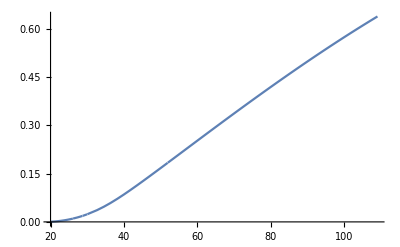

```mathematica
Plot[TakeupTest[a* Pi/180, larm, xleader, yleader, xarm, yarm, rpulley], {a,20, 109}]
```

```mathematica
FullSimplify[Takeup[α,β, Subscript[l, arm], Subscript[x, leader], Subscript[y, leader], Subscript[x, arm], Subscript[y, arm], Subscript[r, pulley]]]
```

(4 π-ArcCos[(2 0.15_pulley)/(√((-Cos[α] l_arm+x_arm)^2+(-Sin[α] l_arm+y_arm)^2))]-ArcCos[(2 0.15_pulley)/(√((-Cos[β] l_arm+x_arm)^2+(-Sin[β] l_arm+y_arm)^2))]-ArcCos[(2 0.15_pulley)/(√((Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2))]-ArcCos[(2 0.15_pulley)/(√((Cos[β] l_arm-x_arm+x_leader)^2+(-Sin[β] l_arm+y_arm+y_leader)^2))]-Mod[2 π+ArcCos[(l_arm^2+x_arm^2-x_arm x_leader+y_arm (y_arm+y_leader)-l_arm (2 Cos[α] x_arm-Cos[α] x_leader+Sin[α] (2 y_arm+y_leader)))/(√(l_arm^2+x_arm^2+y_arm^2-2 l_arm (Cos[α] x_arm+Sin[α] y_arm)) √((Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2))] Sign[ArcTan[(Sin[α] l_arm-y_arm)/Abs[Cos[α] l_arm-x_arm]]-ArcTan[(-Sin[α] l_arm+y_arm+y_leader)/Abs[Cos[α] l_arm-x_arm+x_leader]]],2 π]-Mod[2 π+ArcCos[(l_arm^2+x_arm^2-x_arm x_leader+y_arm (y_arm+y_leader)-l_arm (2 Cos[β] x_arm-Cos[β] x_leader+Sin[β] (2 y_arm+y_leader)))/(√(l_arm^2+x_arm^2+y_arm^2-2 l_arm (Cos[β] x_arm+Sin[β] y_arm)) √((Cos[β] l_arm-x_arm+x_leader)^2+(-Sin[β] l_arm+y_arm+y_leader)^2))] Sign[ArcTan[(Sin[β] l_arm-y_arm)/Abs[Cos[β] l_arm-x_arm]]-ArcTan[(-Sin[β] l_arm+y_arm+y_leader)/Abs[Cos[β] l_arm-x_arm+x_leader]]],2 π]+Mod[2 π-ArcCos[(2 0.15_pulley)/(√((-Cos[α] l_arm+x_arm)^2+(-Sin[α] l_arm+y_arm)^2))]+ArcCos[(-Sin[α] l_arm+y_arm)/(√((-Cos[α] l_arm+x_arm)^2+(-Sin[α] l_arm+y_arm)^2))] Sign[-Cos[α] l_arm+x_arm],2 π]+Mod[2 π-ArcCos[(2 0.15_pulley)/(√((-Cos[β] l_arm+x_arm)^2+(-Sin[β] l_arm+y_arm)^2))]+ArcCos[(-Sin[β] l_arm+y_arm)/(√((-Cos[β] l_arm+x_arm)^2+(-Sin[β] l_arm+y_arm)^2))] Sign[-Cos[β] l_arm+x_arm],2 π]+Mod[2 π-ArcCos[(2 0.15_pulley)/(√((Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2))]+ArcCos[(-Sin[α] l_arm+y_arm+y_leader)/(√((Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2))] Sign[Cos[α] l_arm-x_arm+x_leader],2 π]+Mod[2 π-ArcCos[(2 0.15_pulley)/(√((Cos[β] l_arm-x_arm+x_leader)^2+(-Sin[β] l_arm+y_arm+y_leader)^2))]+ArcCos[(-Sin[β] l_arm+y_arm+y_leader)/(√((Cos[β] l_arm-x_arm+x_leader)^2+(-Sin[β] l_arm+y_arm+y_leader)^2))] Sign[Cos[β] l_arm-x_arm+x_leader],2 π]) 0.15_pulley+√(-4 0.15_pulley^2+l_arm^2+x_arm^2+y_arm^2-2 l_arm (Cos[α] x_arm+Sin[α] y_arm))+√(-4 0.15_pulley^2+l_arm^2+x_arm^2+y_arm^2-2 l_arm (Cos[β] x_arm+Sin[β] y_arm))-2 √(x_leader^2+y_leader^2)+√(-4 0.15_pulley^2+(Cos[α] l_arm-x_arm+x_leader)^2+(-Sin[α] l_arm+y_arm+y_leader)^2)+√(-4 0.15_pulley^2+(Cos[β] l_arm-x_arm+x_leader)^2+(-Sin[β] l_arm+y_arm+y_leader)^2)

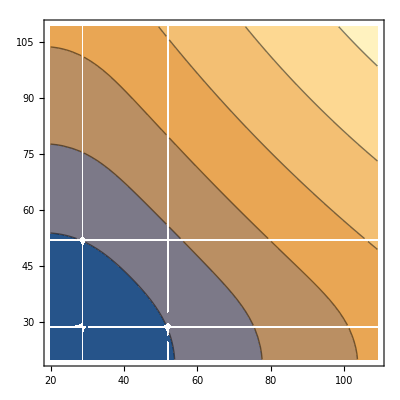

```mathematica
ContourPlot[Takeup[a * Pi /180,b * Pi / 180,larm, xleader, yleader, xarm, yarm, rpulley] , {a, 20, 109}, {b, 20, 109}]
```